### Initialization

```mathematica
Quit
```

```mathematica
Needs["EPToolbox`",NotebookDirectory[]<>"Packages/EPToolbox.m"]
```

```mathematica
Needs["ARMSupport`",NotebookDirectory[]<>"Packages/ARMSupport.m"]
Print[$ARMSupportVersion]
```

ARMSupport v1.0.15, Wed 8 Jun 2016 12:46:18

```mathematica
Needs["MaTeX`",NotebookDirectory[]<>"Packages/MaTeX.m"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts} \\usepackage{lmodern}"}];
```

```mathematica
$OutputDirectory=NotebookDirectory[]<>"../2-ARM-theory/Figures/";
```

#### Automatically save a copy with no output

To turn it on:

```mathematica
SetOptions[
EvaluationNotebook[],
NotebookEventActions->{
{"MenuCommand","Save"}:>(
NotebookSave[];
Block[{nb,tempfile,cleanfile},
tempfile=FileNameJoin[{NotebookDirectory[],"temp.nb"}];
cleanfile=FileNameJoin[{DirectoryName[#],"Clean",StringReplace[FileNameTake[#],{".nb"->" - clean.nb"}]}]&[NotebookFileName[]];
CopyFile[NotebookFileName[],tempfile];
nb=NotebookOpen[tempfile,Visible->False];
NotebookFind[nb,"Output",All,CellStyle];
NotebookDelete[nb];
NotebookSave[nb,cleanfile];
NotebookClose[nb];
Run["sed -i 's/Visible->True/Visible->True/g' ",StringReplace[cleanfile,{" "->"\\ ","\\"->"\\\\"}]];
DeleteFile[tempfile];
]
)
}
];
```

To turn it off:

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{}]
```

#### Carry-over of getIonizationPotential from RBSFA

```mathematica
getIonizationPotential::usage="getIonizationPotential[Target] returns the ionization potential of an atomic target, e.g. \"Hydrogen\", in atomic units.

getIonizationPotential[Target,q] returns the ionization potential of the q-th ion of the specified Target, in atomic units.

getIonizationPotential[{Target,q}] returns the ionization potential of the q-th ion of the specified Target, in atomic units.";

getIonizationPotential[Target_,Charge_:0]:=UnitConvert[(ElementData[Target,"IonizationEnergies"]⟦Charge+1⟧)/(Quantity[1,"AvogadroConstant"]Quantity[1,"Hartrees"])]
getIonizationPotential[{Target_,Charge_:0}]:=getIonizationPotential[Target,Charge]
```

## Saddle-point calculations

### Figure 2A - oscillatory integrand

#### Figure 2A

```mathematica
figure2Aparameters={"Hydrogen",0.053,800,0.5};
```

```mathematica
Block[{tg,Ip,F,λ,ω,p,A,S},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=Integrate[Ip+1/2(p+A[t])^2,t];
figure2A=Plot[
Cos[S[ωt/ω]]
,{ωt,-2π-0.3,3π+0.3}
,MaxRecursion->15
,Frame->True
,PlotRange->{{-2π,3π},{-1,1}}
,PlotRangePadding->{Scaled[.01],Scaled[.05]}
,ImageSize->300
,AspectRatio->1/3
,Axes->None
,FrameStyle->Black
,PlotStyle->{{Darker[Blue,0.2],Thickness[0.004]}}
,FrameTicks->{
{{#,MaTeX[#,FontSize->9]}&/@{-1,0,1},{#,""}&/@{-1,0,1}}
,{
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[-2,3,1/2]
,{#,""}&/@Range[-2π,3π,π/2]}}
,FrameLabel->{MaTeX["\\omega t"],None}
]
]
```

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure2A.pdf",figure2A]]
Export[$OutputDirectory<>"figure2Aparameters.tex",StringJoin[
"\\newcommand{\\figuretwoAtarget}{",ToString[NumberForm[Decapitalize[figure2Aparameters⟦1⟧],2]],"}\n",
"\\newcommand{\\figuretwoAfield}{",ToString[NumberForm[figure2Aparameters⟦2⟧,2]],"}\n",
"\\newcommand{\\figuretwoAlambda}{",ToString[NumberForm[figure2Aparameters⟦3⟧,2]],"}\n",
"\\newcommand{\\figuretwoAmomentum}{",ToString[NumberForm[figure2Aparameters⟦4⟧,2]],"}"
],"Text"];
```

91769

#### Same, but over a complex contour, just for play

```mathematica
Block[{tg,Ip,F,λ,ω,p,A,S},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=Integrate[Ip+1/2(p+A[t])^2,t];
Plot[
Evaluate@ReIm[Exp[ⅈ S[(ωt+1.02ⅈ)/ω]]]
,{ωt,-2π-0.3,3π+0.3}
,MaxRecursion->12
,Frame->True
,PlotRange->{{-2π,3π},Full(*{-1,1}*)}
,PlotRangePadding->{Scaled[.01],Scaled[.05]}
,ImageSize->600
,AxesStyle->Gray,FrameStyle->Black
,Method->{"AxesInFront"->False}
,PlotStyle->{{Darker[Blue,0.2],Thickness[0.003]},{Darker[Red,0.2],Thickness[0.003]}}
,FrameTicks->{
(*{{#,MaTeX[#]}&/@{-1,0,1},{#,""}&/@{-1,0,1}}*)
{Automatic,Automatic}
,{
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}]]}&/@Range[-2,3,1/2]
,{#,""}&/@Range[-2π,3π,π/2]}}
,FrameLabel->{MaTeX["\\omega t"],None}
]
]
```

### Figure 2B - saddle point landscapes and contours

#### Figure 2B

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,midplot,lines,selector
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-2ⅈ,2.25π+2.3ⅈ}
];


midplot=Plot3D[
Im[S[(reωt+ⅈ imωt)/ω]]
,{reωt,-π,2.25π},{imωt,-2,2.3}
,ImageSize->900
,PlotRange->{-70,50}
,ClippingStyle->None
,MeshFunctions->{
Function[{reωt,imωt,ims},Re[S[(reωt+ⅈ imωt)/ω]]]
}
,Mesh->{Re[S[ωt/ω]]/.saddles}
,MeshStyle->{{Black,Thick}}
,MeshShading->{None}
,Lighting->"Neutral"
,PlotPoints->70
];
lines=midplot⟦1,2,1,2,3;;-1⟧;
selector[j_]:=Less[
Min[Flatten[
Outer[
EuclideanDistance,
midplot⟦1,1,lines⟦j,1⟧,{1,2}⟧,
ReIm[ωt]/.saddles,
1
]
]],
0.5
];

figure2B=Show[{
Plot3D[
Im[S[(reωt+ⅈ imωt)/ω]]
,{reωt,-π,2.25π},{imωt,-2,2.3}

(*,ImageSize->1000*)

,ImageSize->350
,PlotRange->{-70,50}
,ClippingStyle->None
,MeshFunctions->{
Function[{reωt,imωt,ims},ims]
,Function[{reωt,imωt,ims},Re[S[(reωt+ⅈ imωt)/ω]]]
}
,Mesh->{Range[-70,50,sp],Range[-500,500,sp]}
,MeshStyle->{{Black},{Black}}
,MeshShading->Transpose[Table[
{{ColorData["M10DefaultDensityGradient"][(s+70)/120]}}
,{s,-70,50,sp}],RotateRight[Range[2]]]
,Lighting->"Neutral"
,ViewPoint->{-3,-0.01,2.1}
,ViewVertical->{0,0,1},ViewRange->All
,Ticks->{
{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9]}&/@Range[-1,2,1/2],
{#,MaTeX[ToString[PaddedForm[#,{2,1}]],FontSize->9]}&/@Range[-2,2,0.5],
{#,MaTeX[ToString[#],FontSize->9]}&/@Range[-60,50,20]}
,AxesLabel->{
Row[{MaTeX["\\mathrm{Re}(\\omega t)",FontSize->11],Spacer[12]}],
MaTeX["\\mathrm{Im}(\\omega t)",FontSize->11],
Row[{Spacer[12],MaTeX["\\mathrm{Im}(S(t))",FontSize->11]}]}

(*,PlotPoints->5*)
,PlotPoints->70
],
Graphics3D[{Thickness[0.004],GraphicsComplex[midplot⟦1,1⟧,lines⟦Select[Range[Length[lines]],selector]⟧]}],
Graphics3D[{
Black,
Ellipsoid[{Re[ωt],Im[ωt],Im[S[ωt/ω]]},{0.05,0.05,4}]/.saddles
}]
}]
]
```

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure2B.pdf",figure2B,ImageSize->350,ImageResolution->600]]
```

523790

### Contours via differential equations

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,midplot,lines,selector
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-2ⅈ,2.25π+2.3ⅈ}
]]⟦2⟧;

ContourPlot[Evaluate[
(Re[S[(reωt+ⅈ imωt)/ω]]==Re[S[ωt/ω]]-0.01)/.saddles
],{reωt,-π/2,π/2},{imωt,-2,2.3}
,ImageSize->400
,AspectRatio->Automatic
,PlotRangePadding->None
]
]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,midplot,lines,selector
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-2ⅈ,2.25π+2.3ⅈ}
]]⟦{1,2}⟧;

Show[{
ContourPlot[Evaluate[Flatten[Table[
(part[S[(reωt+ⅈ imωt)/ω]]==part[S[ωt/ω]])/.saddles
,{part,{Re,Im}}]]]
,{reωt,-π/2,π/2},{imωt,-2,2.3}
(*,PlotRange->{{0.2,0.5},{0.8,1.2}}*)
,ImageSize->400
,PlotPoints->50
,AspectRatio->Automatic
,PlotRangePadding->None
,ContourStyle->{Black,Blue,Darker[Green,0.2],Darker[Red,0.2]}
],
Graphics[{
PointSize[Large],
Point[ReIm[ωt]]/.saddles
}],
Graphics[{
Line[{ReIm[ωt],ReIm[ωt+#]}&[0.3/√(ⅈ S''[ωt/ω])]]/.saddles
}]
}]
]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,midplot,lines,selector
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-2ⅈ,2.25π+2.3ⅈ}
]]⟦1⟧;

Show[{
ContourPlot[Evaluate[Flatten[Table[
(part[S[(reωt+ⅈ imωt)/ω]]==part[S[ωt/ω]])/.saddles
,{part,{Re,Im}}]]]
,{reωt,-π/2,π/2},{imωt,-2,2.3}
(*,PlotRange->{{-0.5,-0.5},{0.8,2.2}}*)
,ImageSize->400
,PlotPoints->50
,AspectRatio->Automatic
,PlotRangePadding->None
,ContourStyle->{Black,Blue,Darker[Green,0.2],Darker[Red,0.2]}
],
VectorPlot[
{-Im[S'[(reωt+ⅈ imωt)/ω]],-Im[ⅈ S'[(reωt+ⅈ imωt)/ω]]}
,{reωt,-π/2,π/2},{imωt,-2,2.3}
(*,PlotRange->{{-0.5,-0.5},{0.8,2.2}}*)
,StreamPoints->Fine
]
}]
]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,midplot,lines,selector
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-2ⅈ,2.25π+2.3ⅈ}
]]⟦{1,2}⟧;

Show[{
ContourPlot[Evaluate[Flatten[Table[
(part[S[(reωt+ⅈ imωt)/ω]]==part[S[ωt/ω]])/.saddles
,{part,{Re,Im}}]]]
,{reωt,-π/2,π/2},{imωt,-2,2.3}
(*,PlotRange->{{-0.5,-0.5},{0.8,2.2}}*)
,ImageSize->400
(*,PlotPoints->50*)
,AspectRatio->Automatic
,PlotRangePadding->None
,ContourStyle->{Black,Blue,Darker[Green,0.2],Darker[Red,0.2]}
],
VectorPlot[
ReIm[-ⅈ S'[(reωt+ⅈ imωt)/ω]*](*{Re[ⅈ S'[(reωt+ⅈ imωt)/ω]],Im[-ⅈ S'[(reωt+ⅈ imωt)/ω]]}*)
,{reωt,-π/2,π/2},{imωt,-2,2.3}
(*,PlotRange->{{-0.5,-0.5},{0.8,2.2}}*)
,StreamPoints->Fine
]
}]
]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,traj
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-0 2ⅈ,2.25π+2.3ⅈ}
]]⟦1⟧;
Table[traj[p,s_]=({reωtt[s],imωtt[s]}/.First@NDSolve[Flatten[{
Thread[{reωtt'[s],imωtt'[s]}==ReIm[-ⅈ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]/Abs[ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]],
Thread[{reωtt[0],imωtt[0]}==(ReIm[ωt+0.001p((1/√(ⅈ S''[ωt/ω]))/(1/Abs[ S''[ωt/ω]]))]/.saddles)]
}]
,{reωtt,imωtt},{s,0,5}]),{p,{-1,1}}];
traj[s_]:=traj[Sign[s+0.0000001],Abs[s]];
ParametricPlot[
traj[s]
,{s,-3,3}
,ImageSize->{{800},{400}}
]

]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,traj
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-0 2ⅈ,2.25π+2.3ⅈ}
]]⟦1⟧;
Table[traj[p,s_]=({reωtt[s],imωtt[s]}/.First@NDSolve[Flatten[{
Thread[{reωtt'[s],imωtt'[s]}==ReIm[-ⅈ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]/Abs[ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]],
Thread[{reωtt[0],imωtt[0]}==(ReIm[ωt+0.001p((1/√(ⅈ S''[ωt/ω]))/(1/Abs[ S''[ωt/ω]]))]/.saddles)]
}]
,{reωtt,imωtt},{s,0,5}]),{p,{-1,1}}];
traj[s_?NumericQ]:=traj[Sign[s+0.0000001],Abs[s]];
Plot[
Abs[Exp[-ⅈ S[(Complex@@traj[s])/ω]]]
,{s,-2,2}
(*,ImageSize->{{800},{400}}*)
,PlotRange->Full
]

]
```

```mathematica
Block[{
tg,Ip,F,λ,ω,p,A,S
,sp=5,saddles,traj
},
{tg,F,λ,p}=figure2Aparameters;
Ip=getIonizationPotential[tg];
ω=45.6/λ;
A[t_]:=-F/ω Sin[ω t];
S[t_]=-Integrate[Ip+1/2(p+A[t])^2,t];


saddles=Sort[FindComplexRoots[
Ip+1/2(p+A[ωt/ω])^2==0
,{ωt,-π-0 2ⅈ,2.25π+2.3ⅈ}
]]⟦1⟧;
Table[traj[p,s_]=({reωtt[s],imωtt[s]}/.First@NDSolve[Flatten[{
Thread[{reωtt'[s],imωtt'[s]}==ReIm[-ⅈ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]/Abs[ S'[(reωtt[s]+ⅈ imωtt[s])/ω]*]],
Thread[{reωtt[0],imωtt[0]}==(ReIm[ωt+0.001p((1/√(ⅈ S''[ωt/ω]))/(1/Abs[ S''[ωt/ω]]))]/.saddles)]
}]
,{reωtt,imωtt},{s,0,5}]),{p,{-1,1}}];
traj[s_?NumericQ]:=traj[Sign[s+0.0000001],Abs[s]];
ParametricPlot[
{{traj[s]⟦1⟧,Re[Exp[-ⅈ S[(Complex@@traj[s])/ω]]]},
{traj[s]⟦1⟧,Im[Exp[-ⅈ S[(Complex@@traj[s])/ω]]]}}
,{s,-2,2}
(*,ImageSize->{{800},{400}}*)
,PlotRange->Full
,AspectRatio->1/2
]

]
```

## SFT plots

### Figure 2C - asymptotics

```mathematica
Quit
```

```mathematica
figure2Cparameters={1,1,2.5,0,0};
figure2Clabel[nx_,nz_]:={"a","b","c","d"}⟦1+nx+2nz⟧
range[0,0]=Range[2,10,2];
range[1,0]=Range[-3,0,1];
range[0,1]=Range[-10,10,5];
range[1,1]=Range[-2,2,2];
drange[0,0]=Range[0,10,0.5];
drange[1,0]=Range[-3,0,0.25];
drange[0,1]=Range[-10,10,1];
drange[1,1]=Range[-3,3,0.5];
```

```mathematica
AbsoluteTiming[
Block[{κ,c,b,po,py,part=Re[#]&,label},
{κ,c,b,po,py}=figure2Cparameters;
label[nx_,nz_]:={"a","b","c","d"}⟦1+nx+2nz⟧;
Table[
figure2C[nx,nz]=Plot3D[
Tooltip[κ a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"]
,{a,1,22},{θ,0,π}
,ImageSize->190
,AxesLabel->{MaTeX["\\vphantom{\\sum^n}a",FontSize->11],Row[{Spacer[5],MaTeX["\\phantom{\\sum}\\theta",FontSize->11]}],""}
(*,PlotLabel->MaTeX["n_x="<>ToString[nx]<>",\ n_z="<>ToString[nz],FontSize->18]*)
,ViewPoint->Scaled/@{2,-1.8,1}
,PlotRangePadding->None
,PlotTheme->"Classic"
,Ticks->{
Join[{#,MaTeX[#,FontSize->9],{0.04,0}}&/@Range[5,20,5],{#,"",{0.02,0}}&/@Range[1,20,1]],
Join[{#,MaTeX[#,FontSize->9],{0.04,0}}&/@Range[0,π,π/6],{#,"",{0.02,0}}&/@Range[0,π,π/24]],
Join[{#,MaTeX[#,FontSize->9],{0.02,0}}&/@range[nx,nz],{#,"",{0.01,0}}&/@drange[nx,nz]]
}
,TicksStyle->Directive[FontFamily->"Latin Modern Math",FontSize->9]
(*,PlotPoints->5*)
,PlotPoints->50
]
,{nx,{0,1}},{ny,{0}},{nz,{0,1}}];
]]
Grid[Transpose[Flatten[Table[
Style[figure2C[nx,nz],Magnification->3]
,{nx,{0,1}},{ny,{0}},{nz,{0,1}}],{1,2}]]]
```

{27.46,Null}

```mathematica
Column[AbsoluteTiming[Table[
FileByteCount[Export[$OutputDirectory<>"figure2C"<>figure2Clabel[nx,nz]<>".pdf",figure2C[nx,nz],ImageSize->190,ImageResolution->800]]
,{nx,{0,1}},{nz,{0,1}}]]]
```

7.10386
{{187249,216679},{332589,236440}}

```mathematica
Export[$OutputDirectory<>"figure2Cparameters.tex",StringJoin[
"\\newcommand{\\figuretwoCkappa}{",ToString[NumberForm[figure2Cparameters⟦1⟧,2]],"}\n",
"\\newcommand{\\figuretwoCc}{",ToString[NumberForm[figure2Cparameters⟦2⟧,2]],"}\n",
"\\newcommand{\\figuretwoCb}{",ToString[NumberForm[figure2Cparameters⟦3⟧,2]],"}\n",
"\\newcommand{\\figuretwoCpo}{",ToString[NumberForm[figure2Cparameters⟦4⟧,2]],"}\n",
"\\newcommand{\\figuretwoCpy}{",ToString[NumberForm[figure2Cparameters⟦5⟧,2]],"}"
],"Text"];
```

### Figure 2D - restricted SFT

```mathematica
figure2Dparameters={1.15,2.5,0.3,10,50};
```

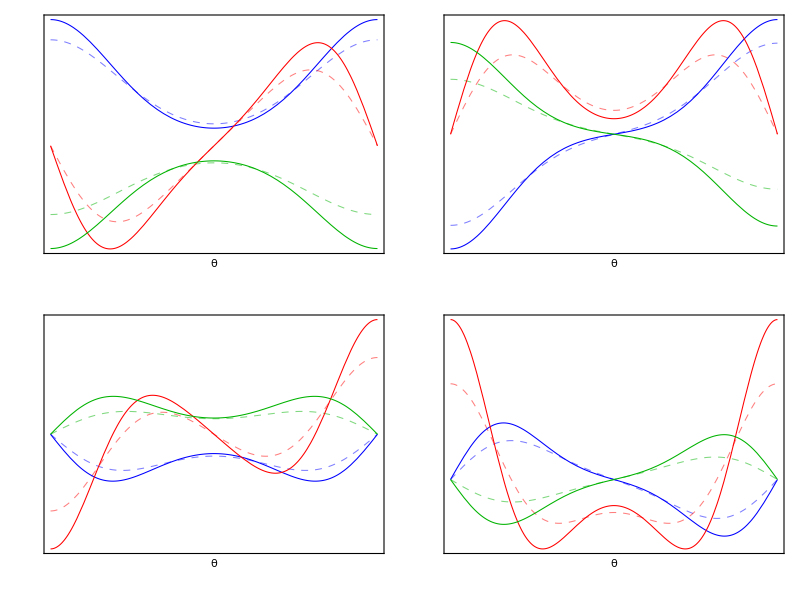

```mathematica
Block[{κ,b,c,a1,a2,th=0.004},
{κ,b,c,a1,a2}=figure2Dparameters;
ClearAll/@DeleteCases[Names["figure2D*"],"figure2Dparameters"];
Grid[
Table[
Evaluate[Symbol["figure2D"<>{"a","b","c","d"}⟦2nx+nz+1⟧]]=Plot[{
a1 ⅇ^(-κ a1)SFTrestricted[θ,κ,a1,b,c,nx,0,nz]
,Evaluate[a1 ⅇ^(-κ a1)Im[SFTderivative[θ,κ,a1,b,c,nx,0,nz]]]
,Evaluate[a1 ⅇ^(-κ a1)Im[SFTpy[θ,κ,a1,b,c,nx,1,nz]]]
,a2 ⅇ^(-κ a2)SFTrestricted[θ,κ,a2,b,c,nx,0,nz]
,Evaluate[a2 ⅇ^(-κ a2)Im[SFTderivative[θ,κ,a2,b,c,nx,0,nz]]]
,Evaluate[a2 ⅇ^(-κ a2)Im[SFTpy[θ,κ,a2,b,c,nx,1,nz]]]
},{θ,0,π/1}
,ImageSize->190
,PlotRange->Full
,PlotStyle->{{Blue,Opacity[0.5],Dashed,Thickness[th]},{Red,Opacity[0.5],Dashed,Thickness[th]},{Darker[Green,0.3],Opacity[0.5],Dashed,Thickness[th]},{Blue,Thickness[th]},{Red,Thickness[th]},{Darker[Green,0.3],Thickness[th]}}
,Frame->True
,PlotRangePadding->{None,Automatic}
,BaseStyle->{{FontFamily->"Latin Modern Math",FontSize->9}}
,FrameTicks->{{
Join[{#,MaTeX[ToString[#],FontSize->9],{0.02,0}}&/@Range[-8,8,2],{#,"",{0.01,0}}&/@Range[-8,8,0.5]],
Join[{#,"",{0.02,0}}&/@Range[-8,8,2],{#,"",{0.01,0}}&/@Range[-8,8,0.5]]
},{
Join[{# π,MaTeX[StringReplace[ToString[Numerator[#]]<>"\\pi/"<>ToString[Denominator[#]],{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}],FontSize->9],{0.02,0}}&/@Range[0,1,1/6],{#,"",{0.01,0}}&/@Range[0,π,π/24]],
Join[{#,"",{0.02,0}}&/@Range[0,π,π/6],{#,"",{0.01,0}}&/@Range[0,π,π/24]]
}}
,ImagePadding->{{15,3},{2+nx 30,1}}
,FrameLabel->{Style["θ",FontFamily->"Latin Modern Math",FontSize->9],""}
]
,{nx,0,1},{nz,0,1}]
(*,PlotLabel->"SFT(0) and -ⅈ(∂SFT)/(∂p_o)(0) at N_y=0,  -ⅈ(∂SFT)/(∂p_y)(0) at N_y=1. κ=1.15, b=2.5, c=0.3, a=30"*)
]
]
```

```mathematica
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure2Da.pdf",figure2Da]]]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure2Db.pdf",figure2Db]]]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure2Dc.pdf",figure2Dc]]]
AbsoluteTiming[FileByteCount[Export[$OutputDirectory<>"figure2Dd.pdf",figure2Dd]]]
Export[$OutputDirectory<>"figure2Dparameters.tex",StringJoin[
"\\newcommand{\\figuretwoDkappa}{",ToString[NumberForm[figure2Dparameters⟦1⟧,2]],"}\n",
"\\newcommand{\\figuretwoDb}{",ToString[NumberForm[figure2Dparameters⟦2⟧,2]],"}\n",
"\\newcommand{\\figuretwoDc}{",ToString[NumberForm[figure2Dparameters⟦3⟧,2]],"}\n",
"\\newcommand{\\figuretwoDaone}{",ToString[NumberForm[figure2Dparameters⟦4⟧,2]],"}\n",
"\\newcommand{\\figuretwoDatwo}{",ToString[NumberForm[figure2Dparameters⟦5⟧,2]],"}"
],"Text"];
```

{0.659946,16045}

{0.846952,15034}

{0.726843,25266}

{0.732205,24199}

```mathematica
Table[
Symbol["figure2D"<>{"a","b","c","d"}⟦2nx+nz+1⟧]
,{nx,0,1},{nz,0,1}]//Grid
```

## Geometry

### Figure 2E - Splitting space

```mathematica
With[{r=√(x^2+y^2+z^2+0.00001),q=40°},
g=ContourPlot3D[
Exp[-1.5r]Cosh[4 z/r]x z
,{x,-3,3},{y,-2.5,2.5},{z,-4.5,4.5}
,Contours->0.15{-1,1}
,Mesh->None
,ContourStyle->{Darker[Red,0.2],GrayLevel[0.6]}
,BoxRatios->Automatic
,PlotPoints->5
,MaxRecursion->1
,ViewPoint->{-1,3, 0}
,ViewVertical->{0, 1, 0}
,Boxed->False
,Axes->False
];

figure2E=Show[{
(*Graphics[{
Inset[Rasterize[g],{0,0},{0.5,0.5},1.2],
}],*)
Graphics[{
Inset[g,{0,0},{0.5,0.5},1.],
Thickness[0.005],
Circle[],
Arrowheads[0.07{-1,1}],
Arrow[{{0,0},{Cos[q],Sin[q]}}],
Inset[MaTeX["a",FontSize->10],0.6{Cos[q],Sin[q]},Scaled[0.7{-1,1}]],
Text[Style["Outer\nregion",10,FontWeight->"Thin",FontFamily->"CMU Serif",LineSpacing->{0, 14}],{1.4,0}],
Text[Style["Inner\nregion",10,FontWeight->"Thin",FontFamily->"CMU Serif",LineSpacing->{0, 14}],{0,-0.6},{0,0}]
}
,ImageSize->180
]
}]
]
FileByteCount[Export[$OutputDirectory<>"figure2E.png",figure2E,ImageResolution->300]]
```

45410

### Figure 2F - Molecular frame geometry

```mathematica
With[{r=√(x^2+y^2+z^2+0.00001),θ=25°,R=7,po=5,py=2.5,pp=10,fs=14},
Framed[
figure2F=Show[{
ContourPlot3D[
Exp[-1.5r]Cosh[4 z/r]x z
,{x,-3,3},{y,-2.5,2.5},{z,-4.5,4.5}
,Contours->0.15{-1,1}
,Mesh->None
,ContourStyle->{{Darker[Red,0.2],Opacity[0.9]},{GrayLevel[0.6],Opacity[0.7]}}
,BoxRatios->Automatic
,PlotPoints->15
,MaxRecursion->1
,Boxed->False
,Axes->False
],
Graphics3D[{
GrayLevel[0.2],Opacity[0.8],Arrowheads[0.035],
Arrow[Tube[{{0,0,0},R{1,0,0}}]],
Arrow[Tube[{{0,0,0},R{0,1,0}}]],
Arrow[Tube[{{0,0,0},R{0,0,1}}]],
Arrow[Tube[{{0,0,0},R{Sin[θ],0,Cos[θ]}}]]
}],
Graphics3D[{
Red,Arrowheads[0.035],
Arrow[Tube[{{0,0,0},pp{Sin[θ],0,Cos[θ]}}]],
Arrow[Tube[{{0,0,0},po{Cos[θ],0,-Sin[θ]}}]],
Arrow[Tube[{{0,0,0},py{0,1,0}}]],
Arrow[Tube[{{0,0,0},po{Cos[θ],0,-Sin[θ]}+py{0,1,0}+pp{Sin[θ],0,Cos[θ]}}]]
}],
Graphics3D[{
Red,Arrowheads[0.025],
Tube[{po{Cos[θ],0,-Sin[θ]},po{Cos[θ],0,-Sin[θ]}+py{0,1,0},py{0,1,0}},0.025],
Arrow[Tube[{{0,0,0},po{Cos[θ],0,-Sin[θ]}+py{0,1,0}},0.025]],
Tube[{(*pp{Sin[θ],0,Cos[θ]},*)po{Cos[θ],0,-Sin[θ]}+py{0,1,0}+pp{Sin[θ],0,Cos[θ]},po{Cos[θ],0,-Sin[θ]}+py{0,1,0}},0.025],
Opacity[0.7],
Tube[{pp{Sin[θ],0,Cos[θ]},po{Cos[θ],0,-Sin[θ]}+pp{Sin[θ],0,Cos[θ]},po{Cos[θ],0,-Sin[θ]}},0.025],
Tube[{po{Cos[θ],0,-Sin[θ]}+pp{Sin[θ],0,Cos[θ]},po{Cos[θ],0,-Sin[θ]}+py{0,1,0}+pp{Sin[θ],0,Cos[θ]}},0.025],
Tube[{pp{Sin[θ],0,Cos[θ]},py{0,1,0}+pp{Sin[θ],0,Cos[θ]},py{0,1,0}},0.025],
Tube[{py{0,1,0}+pp{Sin[θ],0,Cos[θ]},po{Cos[θ],0,-Sin[θ]}+py{0,1,0}+pp{Sin[θ],0,Cos[θ]}},0.025]
}],
Graphics3D[{
GrayLevel[0.3],
Arrow[Tube[Table[5.25{Sin[φ],0,Cos[φ]},{φ,0,θ,5°}],0.02]],
Arrow[Tube[Table[3.25{Cos[φ],0,-Sin[φ]},{φ,0,θ,5°}],0.02]]
}],
Graphics3D[{
Inset[MaTeX["x",FontSize->fs],(R+0.3){1,0,0}],
Inset[MaTeX["y",FontSize->fs],(R+0.3){0,1,0}],
Inset[MaTeX["z",FontSize->fs],(R+0.3){0,0,1}],
Inset[MaTeX["\\hat{\\mathbf u}",FontSize->fs],{0,-0.7,R-0.4}],
Inset[MaTeX["\\hat{\\mathbf n}",FontSize->fs],R{Sin[θ],0,Cos[θ]}+{0.5,0,-0.3}],
Inset[MaTeX["\\theta",FontSize->fs],5.75{Sin[θ/2],0,Cos[θ/2]}],
Inset[MaTeX["\\theta",FontSize->fs],4{Cos[0.45θ],0,-Sin[0.45θ]}],
Inset[MaTeX["\\color{red} \\mathbf{p}",FontSize->fs],1.03(po{Cos[θ],0,-Sin[θ]}+py{0,1,0}+pp{Sin[θ],0,Cos[θ]})],
Inset[MaTeX["\\color{red} \\mathbf{p}_\\perp",FontSize->fs],1.1(po{Cos[θ],0,-Sin[θ]}+py{0,1,0})],
Inset[MaTeX["\\color{red} p_\\mathrm{o}",FontSize->fs],1.1po{Cos[θ],0,-Sin[θ]}],
Inset[MaTeX["\\color{red} p_y",FontSize->fs],py{0,1,0}+{0,-0.2,-0.6}],
Inset[MaTeX["\\color{red} p_\\parallel",FontSize->fs],1.08pp{Sin[θ],0,Cos[θ]}]
}],
Graphics3D[{
Black,
Sphere[{po/Cos[θ],0,0},0.1]
}]
}
,PlotRange->All
,ImageSize->300
,ViewPoint->3{3,-2.9,1.3}
,ViewVertical->{0, 0,1}
]
]
]
```

```mathematica
FileByteCount[Export[$OutputDirectory<>"figure2F.png",figure2F,ImageResolution->300]]
Run["cd "<>$OutputDirectory<>" && convert -trim figure2F.png figure2F.png"]/.{0->"Successful trim"}
```

207814

Successful trim